# VE401 Recitation 3

## Discrete Random Variable

### Hypergeometric Distribution

Purpose: Select n samples from N objects (within which r objects have trait), what is the probability of having x objects with trait?

Parameter and properties:

N∈{0,1,2,...} is the number of total objects.

n∈{0,1,2,...,N} is the number of samples.

r∈{0,1,2,...,N} is the number of objects with traits. p:=r/N,q:=1-p.

E[X] | Var[X] | PDF
n p | n p q (N-n)/(N-1) | Piecewise[{{(Binomial[r, x] Binomial[N-r, n-x])/Binomial[N, n], 0≤x≤N}, {0, otherwise}}]

```mathematica
(* Plot of PDF *)
Manipulate[
DiscretePlot[
PDF[HypergeometricDistribution[Floor[n*Ν],Floor[r*Ν],Ν],x],{x,1,Ν},
PlotRange->{0,1},
AxesOrigin->{0,0},
ImageSize->300,
AxesLabel->{"x","f_X(x)"},
PlotLabel->"PDF of Hypergeometric Distribution with N="<>ToString[Ν]<>", r="<>ToString[Floor[r*Ν]]<>", n="<>ToString[Floor[n*Ν]]
],{Ν,{5,10,50,100}},{n,0,1},{r,0,1},Paneled->False]
```

Approximation: if n/N is sufficiently small, it can be approximated by binomial distribution with parameter n and p=r/N.

```mathematica
(* Plot of PDF *)
Manipulate[
DiscretePlot[
{PDF[HypergeometricDistribution[Floor[n*Ν],Floor[r*Ν],Ν],x],PDF[BinomialDistribution[Floor[n*Ν],Floor[r*Ν]/Ν],x]},{x,1,Ν},
PlotRange->{0,1},
AxesOrigin->{0,0},
AxesLabel->{"x","f_X(x)" },
ImageSize->300,
PlotLabel->"PDF of two distributions",
PlotLegends->{"Hypergeometric distribution\n with N="<>ToString[Ν]<>", r="<>ToString[Floor[r*Ν]]<>", n="<>ToString[Floor[n*Ν]],"Binomial distribution\n with n="<>ToString[Floor[n*Ν]]<>", p="<>ToString[N[Floor[r*Ν]/Ν]]}
],{Ν,{5,10,50,100}},{n,0,1},{r,0,1},Paneled->False]
```

Example:

##### I have a batch of 1000 products, within which 5 are defective. My friend said that he will not accept the batch if there are more than 1% of products that are defective. If he is collecting 100 samples, what is the probability of my batch being falsely rejected?

1-P[X≤1]=1-∑_(x=0)^1 ((5
x)(995
100-x))/(1000
100)=1-91.898%=8.102%

Or we can use the binomial approximation,

1-P[X≤1]=1-∑_(x=0)^1 (100
x)(0.005)^x(0.995)^(100-x)=1-91.018%=8.982%

### Summary

## Continuous Random Variables

### Chi-squared Distribution

Purpose: how is the sum of squares of γ independent standard normal random variables distributed?

Parameter and properties:

γ∈ℕ^+ is the degrees of freedom.

Mean | Variance | PDF | MGF
γ | γ^2 | Piecewise[{{1/(γ/2 2^(γ/2)) x^(γ/2-1)e^(-x/2), x>0}, {0, True}}] | (1-2 t)^(-γ/2)

```mathematica
Manipulate[
Plot[PDF[ChiSquareDistribution[Floor[γ]],x],{x,-1,10},
PlotRange->{0,1},
Filling->Bottom,
AxesOrigin->{0,0},
ImageSize->300,
AxesLabel->{"x","f_X(x)"},
PlotLabel->"PDF of Chi-squared Distribution with γ="<>ToString[Floor[γ]]
],{γ,1,10},
Paneled->False]
```

### Chebyshev Inequality

Purpose: To (roughly) estimate the variance of a random variable.

Mathematical representation: for k∈ℕ\{0}, P[|X|≥c]≤E[|X|^k]/c^k.

Application: P[|X-μ|≥m σ]≤1/m^2.

### Reliability

To study the reliability of a system, we have the following:

Failure density f(t)=lim_(Δt→0) P[t≤T≤t+Δt]/Δt, the probability of failing at time t, (uniform, Weibull, ...)

reliability function R(t)=1-F(t), the probability of system still working at time t,

hazard rate ρ(t)=lim_(Δt→0) P[t≤T≤t+Δt|T≥t]/Δt=(f(t))/(R(t)), the rate of failing at time t given that it didn’t fail before t.

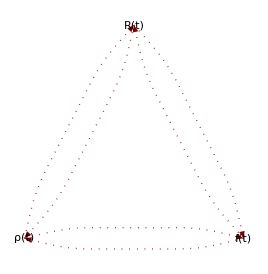

```mathematica
TreePlot[{{"R(t)"->"ρ(t)","ρ(t)=-(R'(t))/(R(t))"},{"ρ(t)"->"R(t)","R(t)=exp(-∫_0^t ρ(x)ⅆx)"},{"R(t)"->"f(t)","f(t)=-R '(t)"},{"f(t)"->"R(t)","R(t)=1-F(t)"},{"ρ(t)"->"f(t)","f(t)=ρ(t)R(t)"},{"f(t)"->"ρ(t)","ρ(t)=(f(t))/(1-F(t))"}},DirectedEdges->True,VertexLabeling->True,PlotStyle->Dotted] /.Inset[a_,b_,c_,d_,DIR_,opts__]:>Inset[a,b,c,d,opts,Background->White]
```

For series system, all components still working ⇒ system still working. R_S(t)=P[all components still working]=∏_(i=1)^k R_i(t).

For parallel system, at least one component still working ⇒ system still working. R_S(t)=P[not all components broken]=1-∏_(i=1)^k (1-R_i(t)).

Example:

##### Your professor has announced that we will have a quiz on Monday class (just an example! not real!), but you don’t know the exact time. What is the probability of not having a quiz in the first 45 minutes? Assume that a class is non-stop and 90 minutes long.

We can use uniform distribution to describe the “failure” density,

f(t)=Piecewise[{{1/90, if 0≤t≤90}, {0, otherwise}}]

And the reliability at time t=45 is

R(t)=1-F(t)=1-t/90=0.5

##### what is the expected rate of your professor giving the quiz at the very next moment?

The hazard rate at t=45 can be calculated as

ρ(t)=(f(t))/(1-F(t))=(1/90)/(1-t/90)=(1/90)/(1-45/90)=1/45

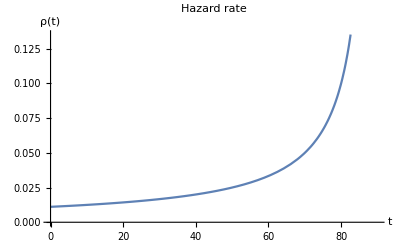

```mathematica
Plot[(1/90)/(1-t/90),{t,0,90},AxesOrigin->{0,0},AxesLabel->{"t","ρ(t)"},PlotLabel->"Hazard rate"]
```

### Weibull Distribution

Purpose: To represent a failure density f(t).

Parameters and properties:

α,β>0.

the hazard rate is Piecewise[{{constant, if β=1}, {increasing, if β>1}, {decreasing, if β<1}}].

Mean | Variance | PDF
α^(-1/β) 1+1/β | α^(-2/β) (1+2/β-(1+1/β)^2) | Piecewise[{{αβ x^(β-1)e^(-α x^β), x>0}, {0, True}}]

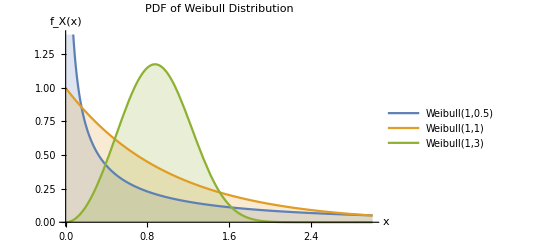

```mathematica
Plot[Table[PDF[WeibullDistribution[β,1^(-1/β)],x],{β,{0.5,1,3}}]//Evaluate,{x,0,3},Filling->Axis,PlotLegends->{"Weibull(1,0.5)","Weibull(1,1)","Weibull(1,3)"},AxesLabel->{"x","f_X(x)"},PlotLabel->"PDF of Weibull Distribution"]
```

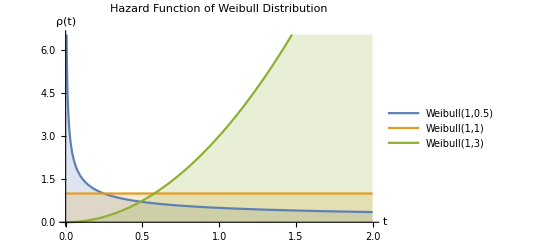

```mathematica
Plot[Table[HazardFunction[WeibullDistribution[β,1^(-1/β)],x],{β,{0.5,1,3}}]//Evaluate,{x,0,2},Filling->Axis,PlotLegends->{"Weibull(1,0.5)","Weibull(1,1)","Weibull(1,3)"},AxesLabel->{"t","ρ(t)"},PlotLabel->"Hazard Function of Weibull Distribution"]
```

### Summary

## Joint Distributions

### Discrete Multivariate Random Variables and its Properties

A discrete multivariate random variable is a map X:S→Ω with a PDF f_X:Ω→ℝ such that

f_X(x,y)≥0 for all x=(x_1,...,x_n)∈Ω,

∑_(x∈Ω) f_X(x)=1.

where f_X(x)=P[X=x=(x_1,...,x_n)]. The marginal density for X is f_X(x)=∑_y f_XY(x,y).

```mathematica
DiscretePlot3D[PDF[MultivariatePoissonDistribution[3,{1,1}],{t,u}],{t,0,10},{u,0,10},ExtentSize->Full,PlotLabel->"Bivariate Poisson Distribution with mean vector λ={4,4}",AxesLabel->{"x","y","f_XY(x,y)"},ColorFunction->"DarkRainbow",ImageSize->370]
```

-Graphics3D-

Example:

##### Let X, Y be random variables such that their PDF looks like f_XY(x,y) | y=-1 | y=0 | y=1 | f_X(x) x=0 | 0 | 1/3 | 0 | x=1 | 1/3 | 0 | 1/3 | f_Y(y) | | | | , calculate the marginal density f_X(x) and f_Y(y).

The marginal density is easily calculated as
 f_XY(x,y) | y=-1 | y=0 | y=1 | f_X(x)
x=0 | 0 | 1/3 | 0 | 1/3
x=1 | 1/3 | 0 | 1/3 | 2/3
f_Y(y) | 1/3 | 1/3 | 1/3 | 1

### Continuous Multivariate Random Variables and its Properties

A continuous multivariate random variable is a map X:S→ℝ^2 with a PDF f_XY:ℝ^2→ℝ such that

f_X(x)≥0 for all x=(x_1,...,x_n)∈ℝ^n,

∫_(ℝ^n) f_X(x)ⅆx=1.

where P[X∈Ω]=∫_Ω f_X(x)ⅆx. 
The marginal density for X is f_X_k(x_k)=∫_(ℝ^(n-1)) f_X(x)ⅆ x_1...ⅆ x_(k-1)ⅆ x_(k+1)...ⅆ x_n.

```mathematica
Plot3D[PDF[BinormalDistribution[{-1,1},{1,2},0],{x,y}],{x,-5,5},{y,-5,5},ColorFunction->"DarkRainbow", PlotStyle->Directive[Opacity[0.5],Red],PlotPoints->40,PlotRange->{0,0.1},PlotLabel->"Bivariate Normal Distribution with μ={-1,1}, σ={1,2}, ρ=0",AxesLabel->{"x","y","f_XY(x,y)"},ImageSize->400]
```

-Graphics3D-

### Independence and Conditional Densities

Comparing two RVs is very analogous to comparing two events.

| Independence | Conditional Probability
two events A and B | P[A∩B]=P[A]P[B] | P[A|B]=P[A∩B]/P[B]
two RVs Xand Y | f_XY(x,y)=f_X(x)f_Y(y)  for all (x,y)∈dom f_XY | f_(X|y)(x)=(f_XY(x,y))/(f_Y(y))

Where f_(X|y)(x)=P[X=x|Y=y].

Example:

##### Let X, Y be random variables such that their PDF looks like f_XY(x,y) | y=-1 | y=0 | y=1 | f_X(x) x=0 | 0 | 1/3 | 0 | 1/3 x=1 | 1/3 | 0 | 1/3 | 2/3 f_Y(y) | 1/3 | 1/3 | 1/3 | 1, calculate P[X=0|Y=1].

This is given by P[X=0|Y=1]=P[X=0 and Y=1]/P[Y=1]=0/(1/3)=0.

### Expectation

Again the properties of expectation of bivariate RVs are similar to RV with single variable.

| Discrete Case | Continuous Case
E[φ∘X] | ∑_(x∈Ω) φ(x)f_X(x) | ∫_(ℝ^n) φ(x)f_X(x) ⅆx
E[X_k] | E[X_k]=∑_(x∈Ω) x_k f_X(x) | E[X_k]=∫_(ℝ^n) x_k f_X(x)ⅆx
E[X_i+X_j] | E[X_i+X_j]=E[X_i]+E[X_j] | 
E[X_i|x_j] | E[X_i|X_j=x_j]=∑_x_i x_i f_(X_i|x_j)(x_j) | E[X_i|X_j=x_j]=∫_(-∞)^∞ x_i f_(X_i|x_j)(x_j)ⅆ x_j

Example:

##### Let X, Y be random variables such that their PDF looks like f_XY(x,y) | y=-1 | y=0 | y=1 | f_X(x) x=0 | 0 | 1/3 | 0 | 1/3 x=1 | 1/3 | 0 | 1/3 | 2/3 f_Y(y) | 1/3 | 1/3 | 1/3 | 1, calculate E[X], E[Y|X=1] and E[X Y].

We have E[X]=0·1/3+1·1/3+1·1/3=2/3, E[Y|X=1]=-1·(1/3)/(2/3)+0·0/(2/3)+1·(1/3)/(2/3)=0 and E[X Y]=-1·1/3+0·1/3+1·1/3=0.

### Covariance

Intuition: The tendency in the linear relationship. Does more X lead to more Y?

Mathematical representation: Simple calculation on the variance of the sum of RV will give

Var[X+Y]=Var[X]+Var[Y]+2E[(X-E[X])(Y-E[Y])]

The extra term will be called the covariance of (X,Y),

Cov[X,Y]=E[(X-μ_X)(Y-μ_Y)]=E[X Y]-E[X]E[Y].

We note that

Cov[X,X]=Var[X],

Cov[X,Y]=E[X Y]-E[X]E[Y]=0 if X and Y are independent. However, the converse is not true. i.e. zero covariance does not imply independence.

Example:

##### Let X,Y be random variables, and Cov[X,Y]=a. What will Cov[2X,2Y] be?

Simple calculation shows that

Cov[2X,2Y]=E[4X Y]-E[2X]E[2Y]=4E[X Y]-4E[X]E[Y]=4a

So the covariance is dependent on the scale of data.

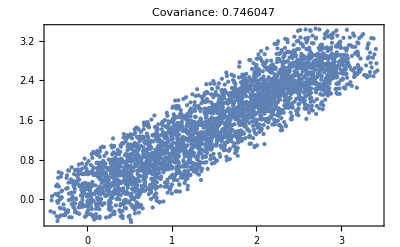
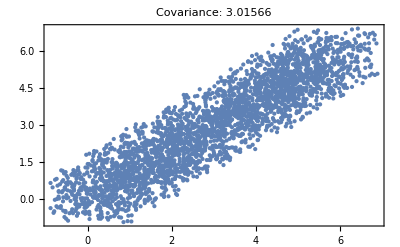

```mathematica
uni=RandomReal[{0,3},3000];
f[x_]:={{x+RandomReal[{-.5,.5}],x+RandomReal[{-.5,.5}]},{2(x+RandomReal[{-.5,.5}]),2(x+RandomReal[{-.5,.5}])}}
data=f/@uni;
Table[ListPlot[data⟦All,i⟧,Frame->True,PlotLabel->Row[{"Covariance: ",Covariance[data⟦All,i⟧]⟦1,2⟧}],PlotStyle->Directive[PointSize[Tiny]]],{i,2}]
```

##### Let X, Y be random variables such that their PDF looks like f_XY(x,y) | y=-1 | y=0 | y=1 | f_X(x) x=0 | 0 | 1/3 | 0 | 1/3 x=1 | 1/3 | 0 | 1/3 | 2/3 f_Y(y) | 1/3 | 1/3 | 1/3 | 1, are they independent? Calculate Cov[X,Y].

Since P[x=0 and y=-1]=0 instead of 1/9, X and Y are clearly not independent. However, we have μ_X=1/3·0+2/3·1=2/3, μ_Y=1/3·0=0, and

Cov[X,Y]=E[X Y]-E[X]E[Y]
=0-0=0

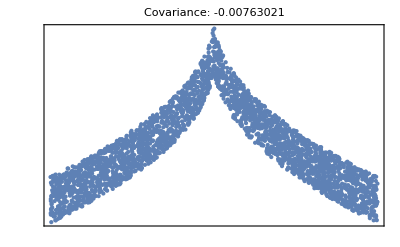
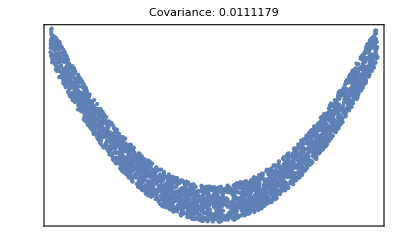
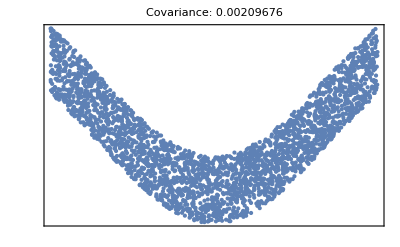
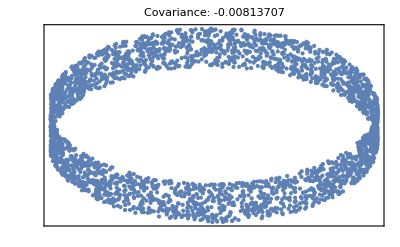

```mathematica
uni=RandomReal[{-3,3},3000];
f[x_]:={{x,-Sqrt[Abs[x]]+RandomReal[.5]},{x,.25 x^2+RandomReal[.5]},{x,-Sinc[x]+RandomReal[.5]},{Cos[x],Sin[x]+RandomReal[.5]}}
data=f/@uni;
Table[ListPlot[data⟦All,i⟧,Frame->True,Axes->None,PlotLabel->Row[{"Covariance: ",Covariance[data⟦All,i⟧]⟦1,2⟧}],PlotStyle->Directive[PointSize[Tiny]],FrameTicks->None],{i,4}]
```

### Covariance Matrix

We define the covariance matrix for a multivariate RV,

Var[X]=(Var[X_1] | Cov[X_1,X_2] | ⋯ | Cov[X_1,X_n]
Cov[X_1,X_2] | Var[X_2] | ⋱ | ⋮
⋮ | ⋱ | ⋱ | Cov[X_(n-1),X_n]
Cov[X_1,X_n] | ⋯ | Cov[X_(n-1),X_n] | Var[X_n])

Properties:

Covariance matrix is symmetric.

For any constant n×n matrix with real coefficient C∈Mat(n×n;ℝ), Var[C X]=C Var[X]C^T.

Example:

##### Let X, Y be random variables such that their PDF looks like f_XY(x,y) | y=-1 | y=0 | y=1 | f_X(x) x=0 | 0 | 1/3 | 0 | 1/3 x=1 | 1/3 | 0 | 1/3 | 2/3 f_Y(y) | 1/3 | 1/3 | 1/3 | 1, calculate the covariance matrix Var[(X,Y)].

We can first calculate

Var[X]=E[(X-μ_X)^2]=1/3(0-2/3)^2+2/3(1-2/3)^2=2/9
Var[Y]=E[(Y-μ_Y)^2]=1/3(-1-0)^2+1/3(0-0)^2+1/3(1-0)^2=2/3

Therefore we have Var[(X,Y)]=(Var[X] | Cov[X,Y]
Cov[X,Y] | Var[Y])=(2/9 | 0
0 | 2/3).

### Pearson Correlation Coefficient

Purpose: to eliminate the effect of the scale of data on covariance.

Mathematical representation: ρ_XY=Cov[X,Y]/(√(Var[X]Var[Y])).

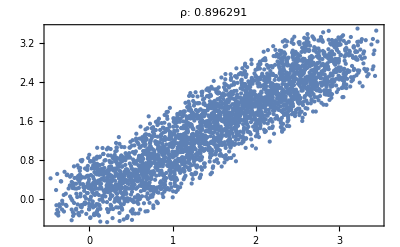
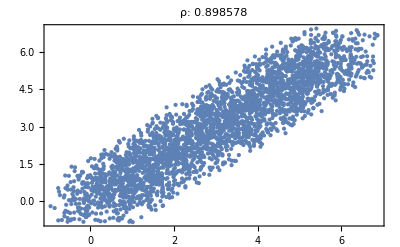

```mathematica
uni=RandomReal[{0,3},3000];
f[x_]:={{x+RandomReal[{-.5,.5}],x+RandomReal[{-.5,.5}]},{2(x+RandomReal[{-.5,.5}]),2(x+RandomReal[{-.5,.5}])}}
data=f/@uni;
Table[ListPlot[data⟦All,i⟧,Frame->True,PlotLabel->Row[{"ρ: ",Correlation[data⟦All,i⟧]⟦1,2⟧}],PlotStyle->Directive[PointSize[Tiny]]],{i,2}]
```

Properties:

-1≤ ρ_XY≤1,

|ρ_XY|=1 indicates perfect linear relationship.

To measure linearity of X and Y, the Fisher transformation 1/2 ln((1+ρ_XY)/(1-ρ_XY))=artanh(ρ_XY) is used. If |artanh(ρ_XY)|→∞ or |ρ_XY|→1, then it indicates linear relationship of X and Y.

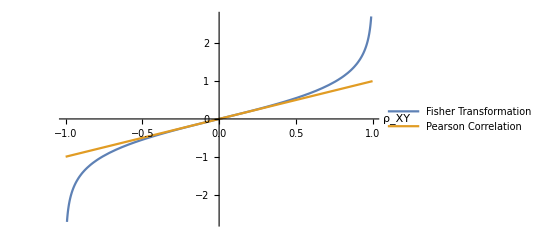

```mathematica
Plot[{ArcTanh[x],x},{x,-1,1},PlotLegends->{"Fisher Transformation","Pearson Correlation"},AxesLabel->{"ρ_XY"}]
```

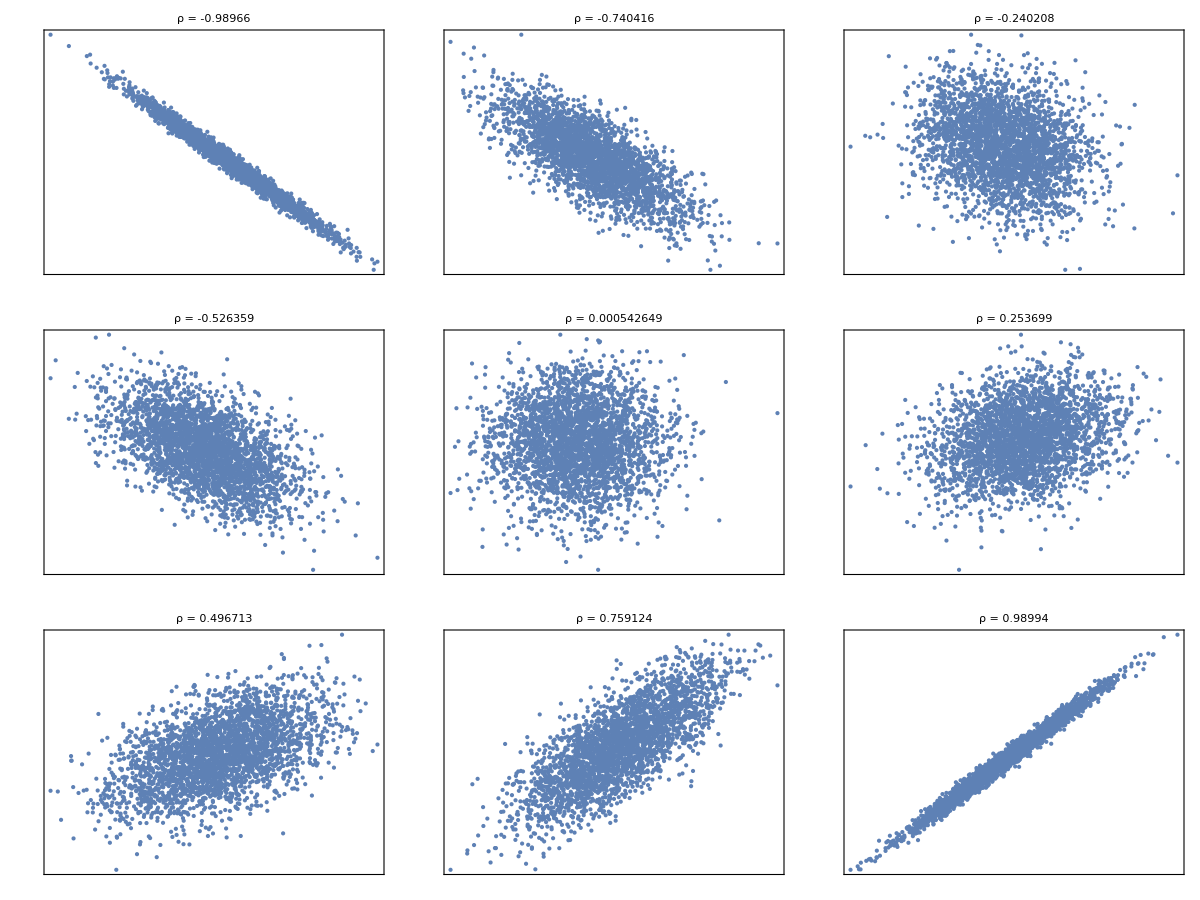

```mathematica
data=BlockRandom[SeedRandom[1];Table[RandomVariate[BinormalDistribution[i],3000],{i,{-.99,-.75,-.25,-.5,0.,.25,.5,.75,.99}}]];
Grid[Partition[Table[ListPlot[i, PlotStyle -> Directive[PointSize[Tiny]], 
     FrameTicks -> None, Frame -> True, Axes -> None,PlotLabel -> Row[{"ρ = ", Correlation[i]⟦1,2⟧}]], {i, data}], 
   3]]
```

### Bivariate Normal Distribution

Purpose: Combine two normal distributed RVs together.

Parameter and properties:

μ_X,μ_Y are the expectation of X and Y, respectively.

σ_X,σ_Y are the standard deviation of X and Y, respectively.

-1<ϱ<1 is the covariance of X and Y.

Mean | Variance | PDF
E[X]=μ_X
E[Y]=μ_Y | Var[X]=σ_X
Var[Y]=σ_Y | 1/(2 πσ_X σ_Y √(1-ϱ^2))exp(-1/(2(1-ϱ^2))[((x-μ_X)/σ_X)^2-2ϱ((x-μ_X)/σ_X)((y-μ_Y)/σ_Y)+((y-μ_Y)/σ_Y)^2])

The conditional mean of Y is linearly dependent on x, E[Y|x]=μ_Y+ϱ σ_Y/σ_X(x-μ_X). Taking μ_X=μ_Y=0 and σ_X=σ_Y=1 we have E[Y|x]=ϱ x.

```mathematica
Manipulate[Plot3D[PDF[BinormalDistribution[{0,0},{1,1},ρ],{x,y}],{x,-5,5},{y,-5,5},ColorFunction->"DarkRainbow", PlotStyle->Directive[Opacity[0.5],Red],PlotPoints->40,PlotRange->{0,0.3},PlotLabel->"Bivariate Normal Distribution with μ={0,0}, σ={1,1}, ρ="<>ToString[ρ],
AxesLabel->{"x","y","f_XY(x,y)"},ImageSize->400],{ρ,-.8,.8},Paneled->False]
```

### Transformation of Variables

Let ((X,Y),f_XY) be continuous bivariate random variable and φ:ℝ^2→ℝ^2 be differentiable bijective map with inverse φ^-1, then (U,V)=φ∘(X,Y) is a continuous bivariate random variable with

f_UV(u,v)=f_XY∘φ^-1(u,v)·|det Dφ^-1(u,v)|

where D φ^-1(u,v)=((∂x)/(∂u) | (∂x)/(∂v)
(∂y)/(∂u) | (∂y)/(∂v)) is the Jacobian of φ^-1.

## Problems for Discussion

### Transformation of Variables: Sum of Two Independent Random Variables

Problem: Given two independent random variables X, Y, and their PDF f_X(x), f_Y(y), how is Z=X+Y distributed? We will start by investigating easier examples.

#### Discrete Case: Rolling Dice

Let X and Y denote the outcome of rolling a die. That is,

f_X(x)=f_Y(x)=Piecewise[{{1/6, if x=1,2,3,4,5,6}, {0, otherwise}}]

Calculate P[Z=2], P[Z=3] and P[Z=4].

##### Solution

P[Z=2]=P[X=1]P[Y=1]=1/6·1/6=1/36
P[Z=3]=P[X=1]P[Y=2]+P[X=2]P[Y=1]=2/36

And similarly, P[Z=4]=P[X=1]P[Y=3]+P[X=2]P[Y=2]+P[X=3]P[Y=1]=3/36.

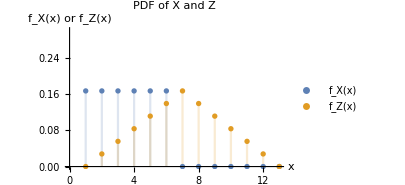

```mathematica
TF=TransformedDistribution[A+B,{A\[Distributed]DiscreteUniformDistribution[{1,6}],B\[Distributed]DiscreteUniformDistribution[{1,6}]}];
DiscretePlot[
{PDF[DiscreteUniformDistribution[{1,6}],x],PDF[TF,x]},{x,1,13},
PlotRange->{0,0.3},
AxesOrigin->{0,0},
ImageSize->300,
AxesLabel->{"x","f_X(x) or f_Z(x)"},
PlotLegends->{"f_X(x)","f_Z(x)"},
PlotLabel->"PDF of X and Z"
]
```

In fact, you have proved in assignment 2 that

P[Z=z]=∑_(x+y=z) P[X=x]P[Y=y]=∑_(y=-∞)^∞ f_X(z-y)f_Y(y)

We notice that this is actually the discrete convolution of f_X and f_Y.

#### Continuous Case: Sum of Uniform Distributed RVs

Let X and Y be identical independent uniform distributed random variables, such that

f_X(x)=f_Y(x)=Piecewise[{{1, if 0≤x≤1}, {0, otherwise}}]

What is the distribution of Z?

##### Solution

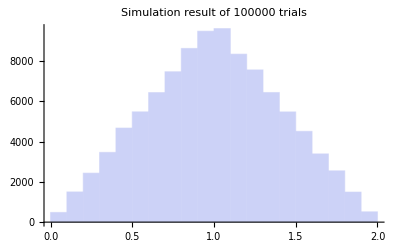

```mathematica
Histogram[RandomReal[1,100000]+RandomReal[1,100000],PlotTheme->"Classic",PlotLabel->"Simulation result of 100000 trials"]
```

It looks like a triangular PDF. Let us verify this. We define (u
v)=φ(x,y):=(x+y
y), then (x
y)=φ^-1(u,v)=(u-v
v). Therefore, the Jacobian of φ^-1 is

D φ^-1(u,v)=((∂x)/(∂u) | (∂x)/(∂v)
(∂y)/(∂u) | (∂y)/(∂v))= ((∂u-v)/(∂u) | (∂u-v)/(∂v)
(∂v)/(∂u) | (∂v)/(∂v))=(1 | -1
0 | 1)

and its determinant is 1. As a result,

f_UV(u,v)=f_XY∘φ^-1(u,v)·|det D φ^-1(u,v)|
=f_XY(u-v,v)
=f_X(u-v)f_Y(v)

Calculating marginal density and replacing u with z,

f_Z(z)=f_U(z)=∫_(-∞)^∞ f_X(z-v)f_Y(v)ⅆv=(f_X*f_Y)(z)

So we can conclude that f_Z is actually the convolution of f_X and f_Y. From this we can easily calculate

f_Z(z)=Piecewise[{{z, if 0≤z≤1}, {2-z, if 1<z≤2}, {0, otherwise}}]

which matches our experiment.

#### Application: Moment Generating Functions of Sum of Independent RVs

If X and Y are independent and moment generating function for X and Y are m_X(t) and m_Y(t), respectively, calculate m_Z(t).

##### Solution

m_Z(t)=E[e^(t Z)]
=∫_(-∞)^∞ e^(z t)f_Z(z)ⅆz
=∫_(-∞)^∞ e^(z t)∫_(-∞)^∞ f_X(z-v)f_Y(v)ⅆvⅆz
=∫_(-∞)^∞ ∫_(-∞)^∞ e^((z -v)t)f_X(z-v)e^(v t)f_Y(v)ⅆvⅆz
=∫_(-∞)^∞ ∫_(-∞)^∞ e^(x t)f_X(x)e^(y t)f_Y(y)ⅆyⅆx                   (x:=z-v,y:=v)
=∫_(-∞)^∞ e^(x t)f_X(x)ⅆx ·∫_(-∞)^∞ e^(y t)f_Y(y)ⅆy
=m_X(t)m_Y(t)

#### Application: Sum of Two i.i.d. Exponential Random Variable

Let f_X(x)=f_Y(x)=Piecewise[{{b e^(-b x), if x≥0}, {0, otherwise}}] be two exponential distributed PDF. What is the distribution of Z=X+Y?

##### Solution

Using the convolution property we can calculate that when z≥0,

f_Z(z)=∫_(-∞)^∞ f_X(z-v)f_Y(v)ⅆv
=∫_0^z b e^(-b (z-v))b e^(-b v)ⅆv
=b^2 z e^(-b z)

Recall that gamma distribution has PDF f_U(u)=β^α/(Γ(α))u^(α-1)e^(-β u). We can see that f_Z(z) is actually a PDF of gamma distribution with α=2 and β=b.

##### Another Solution

We have

m_Z(t)=m_X(t)m_Y(t)
=(b/(b-t))^2
=(1-1/b t)^-2

But gamma distribution with parameters α and β has MGF (1-t/β)^-α. Together with the uniqueness of moment generating function, we can conclude that Z follows a gamma distribution with α=2,β=b. This matches our intuition:

time until second arrival=time until first arrival+time until first arrival

given that the rate of arrival remains the same.

```mathematica
Manipulate[
Plot[{PDF[ExponentialDistribution[β],x],PDF[GammaDistribution[2,1/β],x]},{x,-1,5},
PlotRange->{0,1},
Filling->Bottom,
AxesOrigin->{0,0},
ImageSize->300,
AxesLabel->{"x","f_X(x)"},
PlotLegends->{"Exponential(β)","Gamma(2,β)"},
PlotLabel->"Sum of i.i.d. Exponential Distribution with β="<>ToString[β]
],{β,.1,5},
Paneled->False]
```

### Application of Chebyshev Inequality: Weak Law of Large Numbers

Problem: We want to prove that when the number of independent and identical experiment is very large (e.g. flipping a coin 10000 times), then the proportion of trials with A (e.g. heads coming up) occurring will be close to actual probability of A happening (e.g. 0.5),

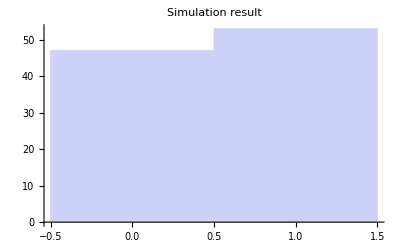

```mathematica
Histogram[RandomInteger[{0,1},100],PlotTheme->"Classic",PlotLabel->"Simulation result"]
```

P[|(number of times A occurs)/(number of times experiment is performed)-P[A]|≥ε ]⟶^(n→∞)0   for any ε>0.

We can denote X_1,...,X_n as n i.i.d. Bernoulli random variable with mean μ=p and variance σ^2=p q to represent n experiments, where P[X_i=1]=P[A occuring on i^th experiment], then

(number of times A occurs)/(number of times experiment is performed)=(X_1+...+X_n)/n

and P[A]=μ=p.

##### Proof

Let X:=(number of times A occurs)/(number of times experiment is performed)-P[A]=(X_1+...+X_n)/n-μ. We have

E[X]=E[(X_1+...+X_n)/n-μ]=(n μ)/n-μ=0

and

Var[X]=Var[(X_1+...+X_n)/n]=(n σ^2)/n^2=σ^2/n

Therefore, E[X^2]=Var[X]+E[X]^2=σ^2/n. Using Chebyshev’s Inequality with k=2,

P[|X|≥ε]≤σ^2/(n ε^2)⟶^(n→∞)0 .

■